```mathematica
SetDirectory[NotebookDirectory[]<>"/../"];
<<SimulationRewardDriven4`;
SetDirectory[NotebookDirectory[]];
(*displays results of simulation*)
PlotBelief1[]:=Module[
{plot,plotforrange1,plotforrange2,data,size},
data=Table[Mean/@BELIEF[[i]],{i,1,BELIEF//Length}];
size=(Length/@data)//Max;
size=nquestionsUSER;
plot=data//ListLinePlot[#,AxesLabel->{Style["j",Large],Style["d",Large]},PlotRange->All,PlotLegends->Table[Style["a= "<>ToString[AffinityValues[[i]]]<>", b="<>ToString[BiasValues[[i]]],Large],{i,1,AffinityValues//Length}],ImageSize->Large,TicksStyle->Directive["Label", 20]]&;
plotforrange1=ListLinePlot[{Join[ConstantArray[-dMAX,size-1],ConstantArray[dMAX,1]]},ImageSize->Large,TicksStyle->Directive["Label", 20],PlotStyle->None];
Print["size=",size];
Show[plotforrange1,plot]
]
```

ν values = {1.,2.66667,21.}

Initialize simulation. 
This sets up the INITIAL values for d,a,b,h which are all lists of size ‘nquestionsUSER’:
- d:  is  the degree of belief on the theory (theory is correct by construction)
- a:  the affinity or tendency for experts to change their belief on the theory, motivated by getting higher rewards.
- b:  is the bias or tendency to reject the objective outcome of experiments, based on their own belief of the theory 
- h:  random walk parameter, associated to the  probability  of experts to change their degree of belief randomly,
          Probability of Random Walk = 2h(1-h)
         examples:  h=0.5   →  50%   ,  h=0.99   →  2% ,  h=1.0   →  0% (no random walk).
The simulation performs a number of experiments given by ‘nexperimentsUSER’. Each experiment asks a number of questions given by  ‘nquestionsUSER’

```mathematica
nquestionsUSER=2000;
nexperimentsUSER=1;
npredictorsUSER=20;
(*affinity related settings, keep fixed*)
RTHRESHOLD=4.04;
NSTABLE=4;
R0=50;
(*bias related settings*)
B0=0.7;
(*set forecast: dmax=4,nsteps=8, max power= 21 ⟹ max{Subscript[p, avg]} = 0.9545 , keep fixed *)
BuildPredictivePowerFunction[4,8];
(*set simulation parameters*)
d=ConstantArray[-dMAX,npredictorsUSER];
a=ConstantArray[5,npredictorsUSER];
b=ConstantArray[0,npredictorsUSER];
h=ConstantArray[0.99,npredictorsUSER];
InitSimulationRewardDriven[d,a,b,h];
```

ν values = {1.,1.58824,2.66667,5.28571,21.}

Run simulation. 
This runs a ‘for-loop’, each iteration corresponds to an experiment. The first iteration uses values set up above for d,a,b,h. 
The degree of belief d is updated according to a,b,h. At the end of every iteration, the values of a,b are changed to be used for the next iteration.
The value of h stays constant during the entire simulation.

```mathematica
For[it=1,it≤nexperimentsUSER,it++,
(*stores values of a,b for all iterations*)
AppendTo[AffinityValues,a//Mean];
AppendTo[BiasValues,b//Mean];
(*to show progress*)
templine=PrintTemporary[Style["it=",Large,Bold],Style[it,Large,Bold]];
(*initialize experiment*)
InitExperimentRewardDriven[d,a,b,h];
(*run experiment*)
RunExperimentStop[];
(*saves data on degree of belief during the simulation*)
StoreBeliefCurrent[];
(*change values of a,b for next iteration, if wanted*)
(*a=ConstantArray[RandomReal[{0.1,5}],npredictors];
b=ConstantArray[RandomReal[{0.1,5}],npredictors];*)
(*deletes display of progress *)
NotebookDelete[templine];
]
EXPERIMENT//Flatten//Cases[x_:>x/;!NumericQ[x]];
Print[Style["This should print a value of 0: value =  ",Large,Bold,Black],Style[%//Length,Bold,Large,Blue]]
```

Plot results
use function ‘PlotBelief1[]’ to see results. Relevant data is stored in the various “superarrays” of ‘EQLab’ and a new one called ‘BELIEF’. After running the initialization step, everything gets wiped out, so please save and organize your progress before running a new simulation.

```mathematica
Length/@BELIEF
PlotBelief1[]
```

# RTHRESHOLD estimation.

```mathematica
rtotal=0;
nruns=10000;
For[it=1,it≤nruns,it++,
dvals=Table[4,{i,1,npredictorsUSER}];
question=blankquestion[];
question[[INDEX["m"]]]=1;
question[[INDEX["v"]]]=ConstantArray[1,npredictorsUSER];
question[[INDEX["q"]]]=1;
question[[INDEX["p"]]]=Table[Random[]//predictivepower[#,question[[INDEX["m"]]],dvals[[i]]]&//Which[#>FORECASTMAX,FORECASTMAX,#<1-FORECASTMAX,1-FORECASTMAX,True,#]&,{i,1,npredictorsUSER}];
question[[INDEX["s"]]]=Surprisal[question];
question[[INDEX["r"]]]=Reward[question];
rtotal+=(question[[INDEX["r"]]]//Apply[Plus]);
]
rtotal
ravg=rtotal/nruns
```

201642.

2.01642

# r0 estimation.

```mathematica
rtotal=0;
nruns=10000;
For[it=1,it≤nruns,it++,
dvals=Table[{-4,4},{i,1,npredictors/2}];dvals=dvals//Flatten;
question=blankquestion[];
question[[INDEX["m"]]]=1;
question[[INDEX["v"]]]=ConstantArray[1,npredictorsUSER];
question[[INDEX["q"]]]=1;
question[[INDEX["p"]]]=Table[Random[]//predictivepower[#,question[[INDEX["m"]]],dvals[[i]]]&//Which[#>FORECASTMAX,FORECASTMAX,#<1-FORECASTMAX,1-FORECASTMAX,True,#]&,{i,1,npredictorsUSER}];
question[[INDEX["s"]]]=Surprisal[question];
question[[INDEX["r"]]]=Reward[question];
rtotal+=(question[[INDEX["r"]]]//Apply[Plus]);
]
rtotal
ravg=rtotal/nruns
```

999057.

99.9057

# Baseline version

#### (Version3) 1) d from -4 to 4 in unit steps 2) h=0.99 : (at end top/bottom , prob for bounce down/up is the same as in between) 3) dinit={-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4,-4} (20 experts) 4) pmax = 0.99 5) power_max : νmax=21 ( ~ 2 σ) 6) ν values = {1.`,1.588235294117647`,2.6666666666666665`,5.285714285714286`,21.`} ( powers in forecast functions ) corresponds to avg forecasts of : {0.5,0.613636,0.727273,0.840909,0.954545 (close to 2σ)} 7) experts=20 8) x=1/2,y=1/2 (large reward average) 9) r0=50 10) r_(total,j)<r_threshold=4.04, n_stable=4, n_max=2000, r0=50 11) b0=0.7 (first version in draft)

{499,568,440,584,355,728,333,375,444,443}

size=2000

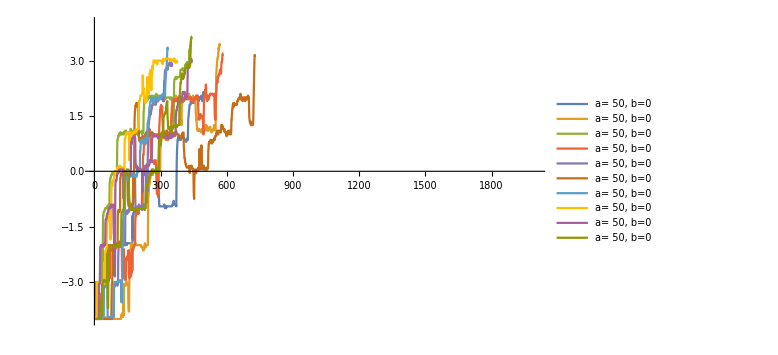

{1058,404,491,692,422,405,972,537,1130,428}

size=2000

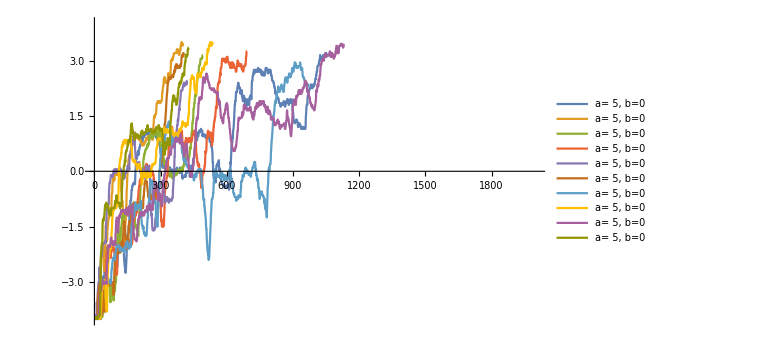

{819,2000,735,644,864,652,1230,1497,1777,480}

size=2000

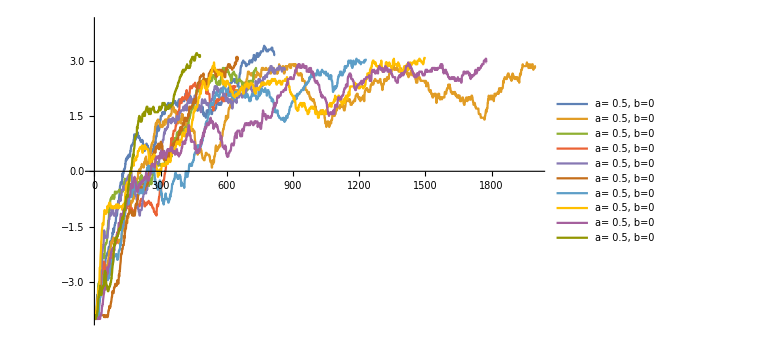

{2000,2000,2000,2000,1782,2000,2000,2000,2000,2000}

size=20004

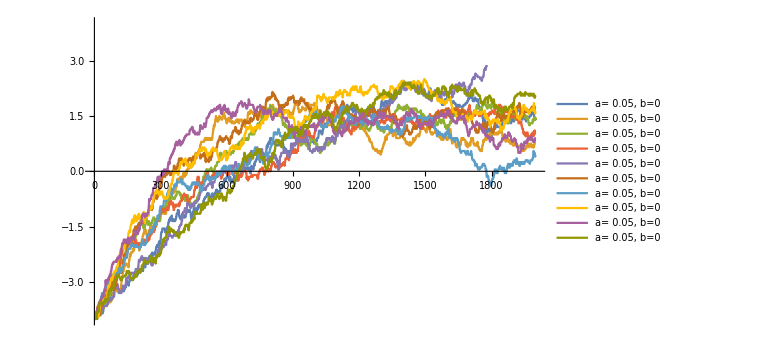

{2000,2000,2000,2000,2000,2000,2000,2000,2000,2000}

size=2000